```mathematica
circle=Circle[{0,0},1]
```

Circle[{0,0},1]



```mathematica
p1=Graphics[Circle[{0,0},1]]
```

```mathematica
func=Sin[x]Sin[y]
```

Sin[x] Sin[y]

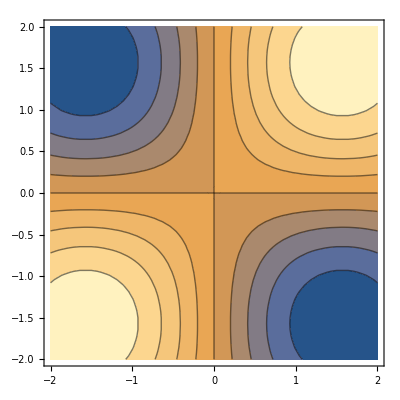

```mathematica
p2=ContourPlot[func,{x,-2,2},{y,-2,2}]
```

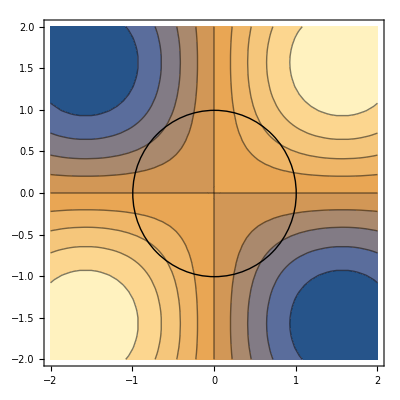

```mathematica
Show[p2,p1]
```

```mathematica
light = FullSimplify[Integrate[func,{x,y}∈Circle[]]]
```

∫_({x,y}∈Circle[{0,0}]) Sin[x] Sin[y]

```mathematica
Evaluate[light]
```

∫_({x,y}∈Circle[{0,0}]) Sin[x] Sin[y]